```mathematica
<<Radia`
```

```mathematica
(* We first set the design criteria for our coils *)

seperation = 60;           (* seperation the coils will have, in mm *)
thickness = 140;           (* axial distance between beginning of first and end of secon coil *)

innerdia = 80;                (* inner diameter of coil *)
outerdia = 160;              (* outer diameter of coil *)

wire = 10;                          (* thickness of the wire in mm *)



(* These set the simulation parameters *)

angres = 80;                      (* number of elements used for simulating the curved areas*)

fieldstrength = 200;    (* desired magnetic field strength in Gauss *)

Temp = 80;                           (* max. temperature at which the coil may operate (in °C)
						only used for determining the resistance of the copper *)
```

```mathematica
(* Create upper coil *)

Upper = radObjRaceTrk[{0.,0.,(seperation+thickness)/4}, {0, (outerdia-innerdia)/2}, {innerdia, innerdia}, (thickness-seperation)/2, angres/4, 1/(wire^2)];

Coils = radObjCnt[{Upper}];


(* Mirror upper coil to create lower coil *)

RadTrfZerPara[Coils, {0,0,0}, {0,0,1}];


(* 3D plot the geometry to find any errors *)

RadPlot3DOptions[];
geo=radObjDrw[Coils];
Show[Graphics3D[geo,PlotLabel->"Geometry",BaseStyle->{14,FontFamily->"Times"}]]
```

-Graphics3D-

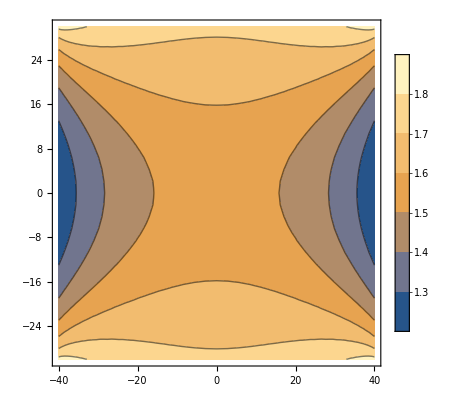

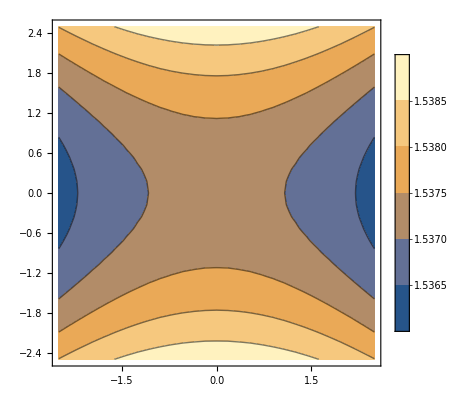

```mathematica
(* calculate the current needed to create the desired field strength at the origin *)

current = fieldstrength/(10000*radFld[Coils, "Bz", {0,0,0}]);


(* Plot the magnetic field in the x-z plane, from coil to coil *)

ContourPlot[10000*radFld[Coils, "Bz", {x,0,z}], {x,-innerdia/2, innerdia/2}, {z, -seperation/2, seperation/2}, PlotLegends->Automatic]


(* Plot the magnetic field in a 5cm x 5 cm area (where the atoms hopefully are) *)

ContourPlot[10000*radFld[Coils, "Bz", {x,0,z}], {x,-2.5, 2.5}, {z, -2.5, 2.5}, PlotLegends->Automatic]
```

```mathematica
(* calculate the resistivity of copper at the operating temperature *)

rho = 1.68*^-8;      (* resistivity of copper at 20°C *)
rhoC = 1.68*^-8+((Temp-20)*1.68*^-8*0.00404);  (* resistivity at operating temperature *)


(* calculate the resistance of the coil at the operating temperature (as well as at 20°C) *)

R = 2*rhoC *4*((innerdia+outerdia)/2)/(wire^4/(((thickness-seperation)/2)*(outerdia-innerdia)/2))*10^3;(* resistance of the coil at operating temperature *)
R0= 2*rho *4*((innerdia+outerdia)/2)/(wire^4/(((thickness-seperation)/2)*(outerdia-innerdia)/2))*10^3 ;   (* resistance of the coil at lab temperature (20°C) *)
```

```mathematica
(* calculate the power dissipated in the coil, using P = R * I.b2 *)

P = current^2*R;


(* calculate the coil system's inductance using the interaction energy *)

L=Abs[radFldEnr[Coils,Coils]];
```

```mathematica
Print["Resistance of coils: ",R," Ohm"];
Print["Inductance of coils: ", N[10^6*L,3]," µH"];

Print["U = ",R*current," V,    I = ",current," A"]
Print["Power dissipated: ",P," W"]

Print["Coil bandwidth = ",(R)/(2*π*L)," Hz"]

Print["B-field at the origin: ", 10000*current*radFld[Coils, "Bz", {0,0,0}]," Gauss"]
```

Resistance of coils: 0.00320599 Ohm

Inductance of coils: 73.8801 µH

U = 0.417132 V,    I = 130.11 A

Power dissipated: 54.2731 W

Coil bandwidth = 6.90644 Hz

B-field at the origin: 200. Gauss